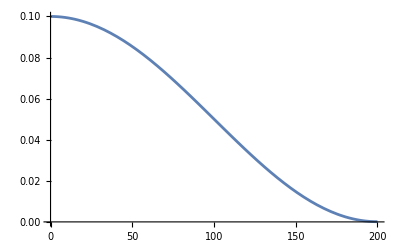

```mathematica
lrmin=0.0001;
lrmax=0.1;
deltalr=lrmax-lrmin;
epochs=200;
lrx[x_]:=lrmin+1/2*deltalr*(1+Cos[x/epochs*π]);
Plot[lrx[x],{x,0,epochs}]
```

```mathematica
(*source: https://medium.com/@theom/a-very-short-visual-introduction-to-learning-rate-schedulers-with-code-189eddffdb00*)
```